```mathematica
Clear[n,F,d,L,ϕ ]
```

```mathematica
(*Steady state*)
```

```mathematica
Pst[x_]:=(F ⅇ^(-(F Abs[x])/d))/(2 d (1-ⅇ^(-(F L)/d)))
```

```mathematica
FullSimplify[Integrate[Pst[x],{x,-L,L},Assumptions->{d>0,F>0,L>0}]]
```

1

```mathematica
(*General solution*)
```

```mathematica
DSolve[F*ϕ'[x]+d*ϕ''[x]==-λ*ϕ[x],ϕ[x],x]
```

{{ϕ[x]→ⅇ^(1/2 x (-F/d-(√(F^2-4 d λ))/d)) C[1]+ⅇ^(1/2 x (-F/d+(√(F^2-4 d λ))/d)) C[2]}}

```mathematica
(*Right (1) and left (2) solutions of x=0, rewritten in terms of sine and cosine*)
```

```mathematica
ϕ1[x_]:=ⅇ^(-(1F)/(2d) x)(c1*Cos[((F √((4 d λ)/F^2-1))/(2d))x] +c2*Sin[((F √((4 d λ)/F^2-1))/(2d))x] )
ϕ2[x_]:=ⅇ^((1F)/(2d) x)(c3*Cos[((F √((4 d λ)/F^2-1))/(2d))x] +c4*Sin[((F √((4 d λ)/F^2-1))/(2d))x] )
```

```mathematica
(*Definition of probability currents on each side.*)
```

```mathematica
J1[x_]:=F*ϕ1[x]+d*ϕ1'[x]
J2[x_]:=-F*ϕ2[x]+d*ϕ2'[x]
```

```mathematica
(*Continuity equations at boundaries and x = 0*)
```

```mathematica
eq1=FullSimplify[ϕ1[L]-ϕ2[-L]]
eq2=FullSimplify[ϕ1[0]-ϕ2[0]]
eq3=FullSimplify[J1[L]-J2[-L]]
eq4=FullSimplify[J1[0]-J2[0]]
```

ⅇ^(-(F L)/(2 d)) ((c1-c3) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]+(c2+c4) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)])

c1-c3

1/2 ⅇ^(-(F L)/(2 d)) F ((c1+c3+(c2-c4) √(-1+(4 d λ)/F^2)) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]+(c2-c4-(c1+c3) √(-1+(4 d λ)/F^2)) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)])

1/2 F (c1+c3+(c2-c4) √(-1+(4 d λ)/F^2))

```mathematica
(*Coefficient matrix of the linear system*)
```

```mathematica
M=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
M[[1]][[1]]=FullSimplify[eq1/.{c1->1,c2->0,c3->0,c4->0}];
M[[1]][[2]]=FullSimplify[eq1/.{c1->0,c2->1,c3->0,c4->0}];
M[[1]][[3]]=FullSimplify[eq1/.{c1->0,c2->0,c3->1,c4->0}];
M[[1]][[4]]=FullSimplify[eq1/.{c1->0,c2->0,c3->0,c4->1}];
M[[2]][[1]]=FullSimplify[eq2/.{c1->1,c2->0,c3->0,c4->0}];
M[[2]][[2]]=FullSimplify[eq2/.{c1->0,c2->1,c3->0,c4->0}];
M[[2]][[3]]=FullSimplify[eq2/.{c1->0,c2->0,c3->1,c4->0}];
M[[2]][[4]]=FullSimplify[eq2/.{c1->0,c2->0,c3->0,c4->1}];
M[[3]][[1]]=FullSimplify[eq3/.{c1->1,c2->0,c3->0,c4->0}];
M[[3]][[2]]=FullSimplify[eq3/.{c1->0,c2->1,c3->0,c4->0}];
M[[3]][[3]]=FullSimplify[eq3/.{c1->0,c2->0,c3->1,c4->0}];
M[[3]][[4]]=FullSimplify[eq3/.{c1->0,c2->0,c3->0,c4->1}];
M[[4]][[1]]=FullSimplify[eq4/.{c1->1,c2->0,c3->0,c4->0}];
M[[4]][[2]]=FullSimplify[eq4/.{c1->0,c2->1,c3->0,c4->0}];
M[[4]][[3]]=FullSimplify[eq4/.{c1->0,c2->0,c3->1,c4->0}];
M[[4]][[4]]=FullSimplify[eq4/.{c1->0,c2->0,c3->0,c4->1}];
MatrixForm[M]
```

(ⅇ^(-(F L)/(2 d)) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)] | ⅇ^(-(F L)/(2 d)) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)] | -ⅇ^(-(F L)/(2 d)) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)] | ⅇ^(-(F L)/(2 d)) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)]
1 | 0 | -1 | 0
1/2 ⅇ^(-(F L)/(2 d)) F (Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]-√(-1+(4 d λ)/F^2) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)]) | 1/2 ⅇ^(-(F L)/(2 d)) F (√(-1+(4 d λ)/F^2) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]+Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)]) | 1/2 ⅇ^(-(F L)/(2 d)) F (Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]-√(-1+(4 d λ)/F^2) Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)]) | -1/2 ⅇ^(-(F L)/(2 d)) F (√(-1+(4 d λ)/F^2) Cos[(F L √(-1+(4 d λ)/F^2))/(2 d)]+Sin[(F L √(-1+(4 d λ)/F^2))/(2 d)])
F/2 | 1/2 F √(-1+(4 d λ)/F^2) | F/2 | -1/2 F √(-1+(4 d λ)/F^2))

```mathematica
FullSimplify[Det[M]]
```

2 d ⅇ^(-(F L)/d) λ (-1+Cos[(F L √(-1+(4 d λ)/F^2))/d])

```mathematica
(*We have the null eigenvalue and the eigenvalues given by the equation. Cos[(F L √(-1+(4 d λ)/F^2))/d]=1*)
```

```mathematica
FullSimplify[Solve[(F L √(-1+(4 d λ)/F^2))/d==2*n*π,λ]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{λ→F^2/(4 d)+(d n^2 π^2)/L^2}}

```mathematica
(*We rewrite the system of equations substituting the eigenvalue*)
```

```mathematica
FullSimplify[Dot[M/.λ->F^2/(4 d)+(d n^2 π^2)/L^2,({{c1}, {c2}, {c3}, {c4}})],Assumptions->{n>0,Mod[n,1]==0}]
```

{{(-1)^n (c1-c3) ⅇ^(-(F L)/(2 d))},{c1-c3},{1/2 (-1)^n ⅇ^(-(F L)/(2 d)) F (c1+c3+2 (c2-c4) √(d^2/(F^2 L^2)) n π)},{1/2 F (c1+c3+2 (c2-c4) √(d^2/(F^2 L^2)) n π)}}

```mathematica
(*The eigenvalues are degenerate; there are two eigenfunctions per eigenvalue*)
```

```mathematica
eq1n=FullSimplify[(c1-c3)==0]
eq2n=FullSimplify[(c1+c3+2 (c2-c4) √(d^2/(F^2 L^2)) n π)==0]
```

c1==c3

c1+c3+2 (c2-c4) √(d^2/(F^2 L^2)) n π==0

```mathematica
(*We solve 2 of the constants in terms of the other 2*)
```

```mathematica
sol=FullSimplify[Solve[{eq1n,eq2n},{c1,c2}],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
```

{{c1→c3,c2→c4-(c3 F L)/(d n π)}}

```mathematica
(*We find two eigenfunctions by setting either c3 or c4 to 0 *)
```

```mathematica
ϕ1n1[x_]:=FullSimplify[(ϕ1[x]/.{λ->F^2/(4 d)+(d n^2 π^2)/L^2})/.{sol}][[1,1]]/.c3->0
ϕ2n1[x_]:=FullSimplify[(ϕ2[x]/.{λ->F^2/(4 d)+(d n^2 π^2)/L^2})/.{sol}][[1,1]]/.c3->0
ϕ1n2[x_]:=FullSimplify[(ϕ1[x]/.{λ->F^2/(4 d)+(d n^2 π^2)/L^2})/.{sol}][[1,1]]/.c4->0
ϕ2n2[x_]:=FullSimplify[(ϕ2[x]/.{λ->F^2/(4 d)+(d n^2 π^2)/L^2})/.{sol}][[1,1]]/.c4->0
```

```mathematica
FullSimplify[ϕ1n1[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ2n1[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ1n2[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ2n2[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
```

c4 ⅇ^(-(F x)/(2 d)) Sin[(n π x)/L]

c4 ⅇ^((F x)/(2 d)) Sin[(n π x)/L]

(c3 ⅇ^(-(F x)/(2 d)) (d n π Cos[(n π x)/L]-F L Sin[(n π x)/L]))/(d n π)

c3 ⅇ^((F x)/(2 d)) Cos[(n π x)/L]

```mathematica
(*We uniquely determine the first eigenfunction by normalizing it*)
```

```mathematica
Integrate[(ϕ1n1[x])^2/Pst[x],{x,0,L},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]+Integrate[(ϕ2n1[x])^2/Pst[x],{x,-L,0},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]
```

(2 c4^2 d ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L)/F

```mathematica
solc4=FullSimplify[Solve[(2 c4^2 d ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L)/F==1,c4]]
```

{{c4→-(ⅇ^((F L)/(2 d)) √F)/(√2 √d √(-1+ⅇ^((F L)/d)) √L)},{c4→(ⅇ^((F L)/(2 d)) √F)/(√2 √d √(-1+ⅇ^((F L)/d)) √L)}}

```mathematica
ϕ1f1[x_]:=FullSimplify[ϕ1n1[x]/.solc4[[2]]]
ϕ2f1[x_]:=FullSimplify[ϕ2n1[x]/.solc4[[2]]]
```

```mathematica
FullSimplify[ϕ1f1[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ2f1[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
```

(ⅇ^((F (L-x))/(2 d)) Sin[(n π x)/L])/(√2 √((d (-1+ⅇ^((F L)/d)) L)/F))

(ⅇ^((F (L+x))/(2 d)) Sin[(n π x)/L])/(√2 √((d (-1+ⅇ^((F L)/d)) L)/F))

```mathematica
(*Same for the second one*)
```

```mathematica
Integrate[(ϕ1n2[x])^2/Pst[x],{x,0,L},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]+Integrate[(ϕ2n2[x])^2/Pst[x],{x,-L,0},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]
```

(c3^2 d ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L)/F+(c3^2 ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L (F^2 L^2+d^2 n^2 π^2))/(d F n^2 π^2)

```mathematica
solc3=FullSimplify[Solve[(c3^2 d ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L)/F+(c3^2 ⅇ^(-(F L)/d) (-1+ⅇ^((F L)/d)) L (F^2 L^2+d^2 n^2 π^2))/(d F n^2 π^2)==1,c3],Assumptions->{d>0,F>0,L>0,n>0}]
```

{{c3→-ⅇ^((F L)/(2 d)) n π √((d F)/((-1+ⅇ^((F L)/d)) L (F^2 L^2+2 d^2 n^2 π^2)))},{c3→ⅇ^((F L)/(2 d)) n π √((d F)/((-1+ⅇ^((F L)/d)) L (F^2 L^2+2 d^2 n^2 π^2)))}}

```mathematica
ϕ1f2[x_]:=FullSimplify[ϕ1n2[x]/.solc3[[2]]]
ϕ2f2[x_]:=FullSimplify[ϕ2n2[x]/.solc3[[2]]]
```

```mathematica
FullSimplify[ϕ1f2[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
FullSimplify[ϕ2f2[x],Assumptions->{d>0,n>0,F>0,L>0,Mod[n,1]==0}]
```

(ⅇ^((F (L-x))/(2 d)) √((d F)/((-1+ⅇ^((F L)/d)) L (F^2 L^2+2 d^2 n^2 π^2))) (d n π Cos[(n π x)/L]-F L Sin[(n π x)/L]))/d

ⅇ^((F (L+x))/(2 d)) n π √((d F)/((-1+ⅇ^((F L)/d)) L (F^2 L^2+2 d^2 n^2 π^2))) Cos[(n π x)/L]

```mathematica
(*We check the orthogonality of the eigenfunctions*)
```

```mathematica
Integrate[((ϕ1f2[x])(ϕ1f1[x]))/Pst[x],{x,0,L},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]+Integrate[((ϕ2f2[x])ϕ2f1[x])/Pst[x],{x,-L,0},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]
```

-(F L)/(√2 √(F^2 L^2+2 d^2 n^2 π^2))

```mathematica
(*It's not orthogonal; we apply Gram-Schmidt to obtain a second eigenfunction prime that is orthogonal*)
```

```mathematica
ϕ1f2GS[x_]:=FullSimplify[ϕ1f2[x]+(F L)/(√2 √(F^2 L^2+2 d^2 n^2 π^2))ϕ1f1[x]]
ϕ2f2GS[x_]:=FullSimplify[ϕ2f2[x]+(F L)/(√2 √(F^2 L^2+2 d^2 n^2 π^2))ϕ2f1[x]]
```

```mathematica
(*We normalize the new second eigenfunction*)
```

```mathematica
Integrate[(ϕ1f2GS[x])^2/Pst[x],{x,0,L},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]+Integrate[(ϕ2f2GS[x])^2/Pst[x],{x,-L,0},Assumptions->{F>0,d>0,L>0,Mod[n,1]==0}]
```

(F^2 L^2+4 d^2 n^2 π^2)/(2 (F^2 L^2+2 d^2 n^2 π^2))

```mathematica
ϕ1f2GSf[x_]:=Sqrt[(2 (F^2 L^2+2 d^2 n^2 π^2))/(F^2 L^2+4 d^2 n^2 π^2)]ϕ1f2GS[x]
ϕ2f2GSf[x_]:=Sqrt[(2 (F^2 L^2+2 d^2 n^2 π^2))/(F^2 L^2+4 d^2 n^2 π^2)]ϕ2f2GS[x]
```

```mathematica
FullSimplify[ϕ1f2GSf[x],Assumptions->{F>0,d>0,L>0,n>0,Mod[n,1]==0}]
FullSimplify[ϕ2f2GSf[x],Assumptions->{F>0,d>0,L>0,n>0,Mod[n,1]==0}]
```

(ⅇ^((F (L-x))/(2 d)) (2 √((d^5 F)/L) n π Cos[(n π x)/L]-√(d^3 F^3 L) Sin[(n π x)/L]))/(√2 d^2 √((-1+ⅇ^((F L)/d)) (F^2 L^2+4 d^2 n^2 π^2)))

(ⅇ^((F (L+x))/(2 d)) F (2 d n π Cos[(n π x)/L]+F L Sin[(n π x)/L]))/(√2 √(d (-1+ⅇ^((F L)/d)) F L (F^2 L^2+4 d^2 n^2 π^2)))

```mathematica
(*We plot the eigenfunction*)
```

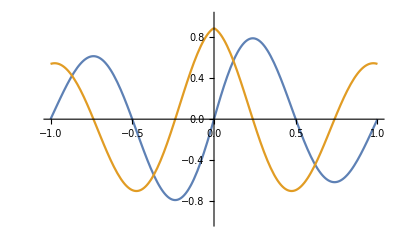

```mathematica
n=2;
F=1;
d=1;
L=1;
Show[Plot[{ϕ1f1[x],ϕ1f2GSf[x]},{x,0,L}],Plot[{ϕ2f1[x],ϕ2f2GSf[x]},{x,-L,0}],PlotRange->{{-L,L},{-1,1}}]
```

```mathematica
c1v[x0_]:=ϕ1f1[x0]/Pst[x0]
c2v[x0_]:=ϕ1f2GSf[x0]/Pst[x0]
F=1;
d=1;
L=1;
x0=0.5;
ncut=200;
Show[Plot[Pst[x]+Sum[c1v[x0]*ϕ1f1[x],{n,1,ncut}]+Sum[c2v[x0]*ϕ1f2GSf[x],{n,1,ncut}],{x,0,L},PlotRange->{{-L,L},{-5,25}}],Plot[Pst[x]+Sum[c1v[x0]*ϕ2f1[x],{n,1,ncut}]+Sum[c2v[x0]*ϕ2f2GSf[x],{n,1,ncut}],{x,-L,0},PlotRange->{{-L,L},{-5,25}}]]
```

-Graphics-